```mathematica
SetDirectory[NotebookDirectory[]];
Get["../source/mathematica/AnalyticValence.wl"];
Get["../source/mathematica/AsymmetricValence.wl"];
Get["../source/mathematica/FigureSettings.wl"];
InitializePlotSettings[]
```

```mathematica
{J,II,V,ϵ}={0.2,0.5,1,0.05};
```

```mathematica
{ϕ1,p1,n1}=r1Results[J,II,V,ϵ];
{ϕ2,p2,n2}=r2Results[J,II,V,ϵ];
{ϕ12,p12,n12}=r12Results[J,II,V,ϵ];
{ϕ13,p13,n13}=AsymmetricValenceResults[1/3,J,II,V,ϵ];
{ϕ3,p3,n3}=AsymmetricValenceResults[3,J,II,V,ϵ];
```

```mathematica
pFuncs=(#[x]&)/@{p3,p2,p1,p12,p13};
nFuncs=(#[x]&)/@{n3,n2,n1,n12,n13};
phiFuncs=(#[x]&)/@{ϕ3,ϕ2,ϕ1,ϕ12,ϕ13};
```

```mathematica
pPlot=Plot[pFuncs,{x,0,1},PlotRange->{{0,1},{0.6,1.6}},PlotStyle->MapThread[Directive,{DivergentColoursv2,dottingv2,Thick1}],Frame->True,AspectRatio->1,ImageSize->400];
nPlot=Plot[nFuncs,{x,0,1},PlotRange->{{0,1},{0.6,1.6}},PlotStyle->MapThread[Directive,{DivergentColoursv2,dottingv2,Thick1}],Frame->True,AspectRatio->1,GridLines->Automatic,ImageSize->400];phiPlot=Plot[phiFuncs,{x,0,1},PlotRange-> {{0,1},{-0.2,1.2}},PlotStyle->MapThread[Directive,{DivergentColoursv2,dottingv2,Thick1}],Frame->True,AspectRatio->1,ImageSize->400];
```

```mathematica
LBLP=Plot[{pFuncs},{x,0,0.1},PlotRange->{{0,0.1},{0.6,1.201}},PlotStyle->MapThread[Directive,{DivergentColoursv2,dottingv2,Thick2}],Frame->True,FrameTicks->{{Table[{y,NumberForm[y,{3,1}]},{y,0.4,1.4,0.1}],Automatic},{Table[{x,NumberForm[x,{3,2}]},{x,0,0.1,0.02}],Automatic}},AspectRatio->1.5,ImageSize->400,GridLines->{Automatic,Range[0.4,2,0.2]}];
```

```mathematica
RBLP=Plot[{pFuncs},{x,0.9,0.9995},PlotRange->{{0.9,1},{0.8,1.801}},PlotStyle->MapThread[Directive,{DivergentColoursv2,dottingv2,Thick2}],Frame->True,FrameTicks->{{Table[{y,NumberForm[y,{3,1}]},{y,0.4,2,0.2}],Automatic},{Table[{x,NumberForm[x,{3,2}]},{x,0.9,1,0.02}],Automatic}},AspectRatio->1.5,ImageSize->400,GridLines->{Automatic,Range[0.4,2,0.2]}];
```

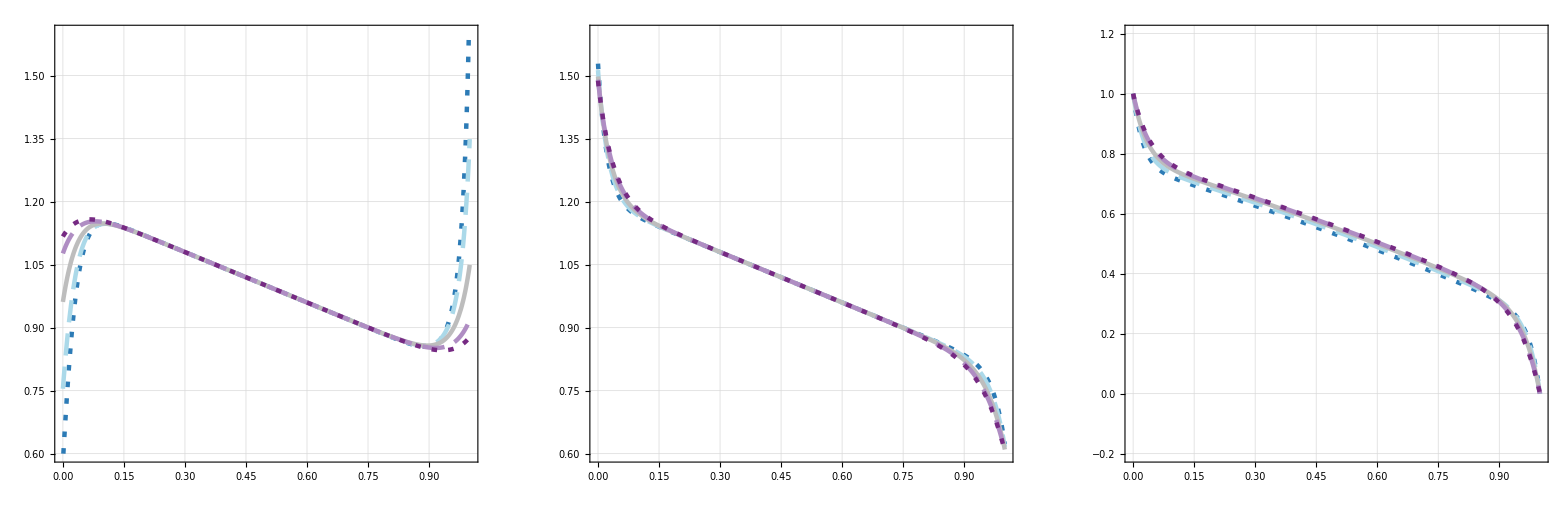

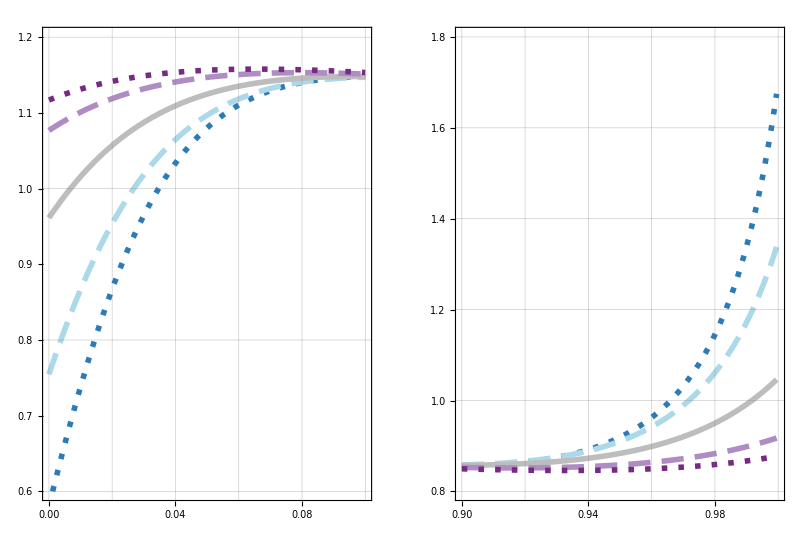

```mathematica
FullPlots=GraphicsRow[{pPlot,nPlot,phiPlot},ImageSize->1600]
BLPlots=GraphicsRow[{LBLP,RBLP},ImageSize->800]
```

Labels and annotations added in photo editing software Canva.

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"..","figures","Figure6a.pdf"}],FullPlots,ImageResolution->300]
Export[FileNameJoin[{NotebookDirectory[],"..","figures","Figure6b.pdf"}],BLPlots,ImageResolution->300]
```

/Users/georginaryan/Desktop/DPhil/Research/Draft Papers/Journal Article - Chapter 4/Figures Ratio Version/Final Code for Repository/asymmetric-valence-electrolytes/notebooks/../figures/Figure6a.pdf

/Users/georginaryan/Desktop/DPhil/Research/Draft Papers/Journal Article - Chapter 4/Figures Ratio Version/Final Code for Repository/asymmetric-valence-electrolytes/notebooks/../figures/Figure6b.pdf